```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["Spins_T_1_h_50_minusK_60_G_30_theta_0.12566370614359174.dat","Table"];
data1=Rest[data](* first row dropped *);
```

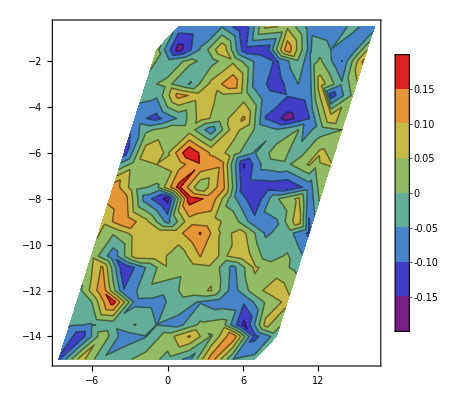

```mathematica
data2=Table[{data1[[i]][[2]],data1[[i]][[3]],data1[[i]][[6]]},{i,1,200,1}];
ListContourPlot[data2,PlotLegends->Automatic,ColorFunction->"Rainbow"]
```